```mathematica
fquart = a T^4 + c T - B
```

-B+c T+a T^4

```mathematica
Needspaclet:ref/Needs["FunctionApproximations`"]
```

RefLink[Needs,paclet:ref/Needs][FunctionApproximations`]

```mathematica
<<FunctionApproximations`
```

```mathematica
era=EconomizedRationalApproximation[fquart,{T,{T0,TR},2,1}]
```

(-B+(c T0)/2+(29 a T0^4)/384+(c TR)/2+19/96 a T0^3 TR+29/64 a T0^2 TR^2+19/96 a T0 TR^3+(29 a TR^4)/384-(5 B T0^2)/(18 (T0+TR)^2)+(5 c T0^3)/(36 (T0+TR)^2)+(5 a T0^6)/(288 (T0+TR)^2)+(5 c T0^2 (T+1/2 (-T0-TR)))/(18 (T0+TR)^2)+(5 a T0^5 (T+1/2 (-T0-TR)))/(36 (T0+TR)^2)+(5 B T0 TR)/(9 (T0+TR)^2)-(5 c T0^2 TR)/(36 (T0+TR)^2)+(5 a T0^5 TR)/(144 (T0+TR)^2)-(5 c T0 (T+1/2 (-T0-TR)) TR)/(9 (T0+TR)^2)+(5 a T0^4 (T+1/2 (-T0-TR)) TR)/(36 (T0+TR)^2)-(5 B TR^2)/(18 (T0+TR)^2)-(5 c T0 TR^2)/(36 (T0+TR)^2)-(5 a T0^4 TR^2)/(288 (T0+TR)^2)+(5 c (T+1/2 (-T0-TR)) TR^2)/(18 (T0+TR)^2)-(5 a T0^3 (T+1/2 (-T0-TR)) TR^2)/(18 (T0+TR)^2)+(5 c TR^3)/(36 (T0+TR)^2)-(5 a T0^3 TR^3)/(72 (T0+TR)^2)-(5 a T0^2 (T+1/2 (-T0-TR)) TR^3)/(18 (T0+TR)^2)-(5 a T0^2 TR^4)/(288 (T0+TR)^2)+(5 a T0 (T+1/2 (-T0-TR)) TR^4)/(36 (T0+TR)^2)+(5 a T0 TR^5)/(144 (T0+TR)^2)+(5 a (T+1/2 (-T0-TR)) TR^5)/(36 (T0+TR)^2)+(5 a TR^6)/(288 (T0+TR)^2)+(4 B (T+1/2 (-T0-TR)))/(3 (T0+TR))+(c T0 (T+1/2 (-T0-TR)))/(3 (T0+TR))+(5 a T0^4 (T+1/2 (-T0-TR)))/(12 (T0+TR))-(4 c (T+1/2 (-T0-TR))^2)/(3 (T0+TR))+(5 a T0^3 (T+1/2 (-T0-TR))^2)/(6 (T0+TR))+(c (T+1/2 (-T0-TR)) TR)/(3 (T0+TR))+(5 a T0^3 (T+1/2 (-T0-TR)) TR)/(3 (T0+TR))+(5 a T0^2 (T+1/2 (-T0-TR))^2 TR)/(2 (T0+TR))+(5 a T0^2 (T+1/2 (-T0-TR)) TR^2)/(2 (T0+TR))+(5 a T0 (T+1/2 (-T0-TR))^2 TR^2)/(2 (T0+TR))+(5 a T0 (T+1/2 (-T0-TR)) TR^3)/(3 (T0+TR))+(5 a (T+1/2 (-T0-TR))^2 TR^3)/(6 (T0+TR))+(5 a (T+1/2 (-T0-TR)) TR^4)/(12 (T0+TR)))/(1+(5 T0^2)/(18 (T0+TR)^2)-(5 T0 TR)/(9 (T0+TR)^2)+(5 TR^2)/(18 (T0+TR)^2)-(4 (T+1/2 (-T0-TR)))/(3 (T0+TR)))

```mathematica
era=RationalInterpolation[Exp[t],{T,2,2},{a,b,(a+b)/2}]
```

RationalInterpolation::notnum: Function is not numerical at the interpolation points: {2.71828^t,2.71828^t,2.71828^t,2.71828^t,2.71828^t}.

RationalInterpolation[ⅇ^t,{T,2,2},{a,b,(a+b)/2}]

```mathematica
Expand[u^2(u^2-2 v)^2]
```

u^6-4 u^4 v+4 u^2 v^2

```mathematica
Expand[(T^2+u T + v)(T^2-u T + w)]
```

T^4-T^2 u^2+T^2 v-T u v+T^2 w+T u w+v w

```mathematica
Expand[u^2(u^2-v-v)^2]
```

u^6-4 u^4 v+4 u^2 v^2

```mathematica
Solve[y^3 - 4 r y -q^2==0,y]
```

{{y→(4 (2/3)^(1/3) r)/((9 q^2+√3 √(27 q^4-256 r^3))^(1/3))+((9 q^2+√3 √(27 q^4-256 r^3))^(1/3))/(2^(1/3) 3^(2/3))},{y→-(2 (2/3)^(1/3) (1+ⅈ √3) r)/((9 q^2+√3 √(27 q^4-256 r^3))^(1/3))-((1-ⅈ √3) (9 q^2+√3 √(27 q^4-256 r^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{y→-(2 (2/3)^(1/3) (1-ⅈ √3) r)/((9 q^2+√3 √(27 q^4-256 r^3))^(1/3))-((1+ⅈ √3) (9 q^2+√3 √(27 q^4-256 r^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
sol=NDSolve[{T'[t] == R (1-T[t]^4) + (1-T[t])/.{R-> 10},T[0]== 0.4},T[t],{t,0,1}]
```

{{T[t]→InterpolatingFunction[…][t]}}

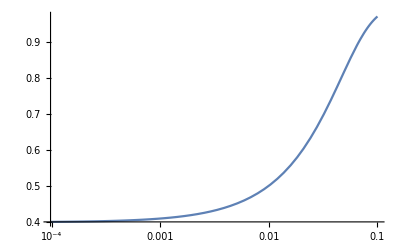

```mathematica
LogLinearPlot[Evaluate[T[t]/.sol],{t,0,.1},PlotRange->All]
```

```mathematica
Troot[R_,t_]:=H/. FindRoot[NIntegrate[1/(1-u+R(1-u^4)),{u,0.4,H}]-t,{H,0.95}]
```

NIntegrate::nlim: u = H is not a valid limit of integration.

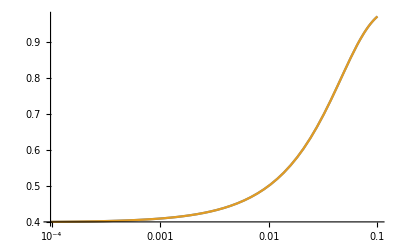

```mathematica
LogLinearPlot[{Troot[10,t],Evaluate[T[t]/.sol]},{t,0,.1},PlotRange->All]
```

```mathematica
Assuming[u0>1&&U>1,Integrate[1/(1-u+R(1-0*u^4)),u]]
```

-Log[1+R-u]

```mathematica
Solve[%==t,u]
```

{{u→ConditionalExpression[1-ⅇ^-t+R, -π≤Im[t]<π]}}

```mathematica
Series[%,{R,0,1}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of 1+4 R+6 R #1+4 R #1^2+R #1^3& for some values of R.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

1/9 (-3 Log[2]+3 Log[-1+ⅈ √3]+3 Log[(-1-ⅈ √3)/(2 R^(1/3))]-2 Log[R]-9 Log[-1+u])-1/(27 ((-ⅈ+√3) (ⅈ+√3)))16 (3 (-1)^(1/3) Log[2]-3 (-1)^(1/3) Log[-1+ⅈ √3]+3 (-1)^(2/3) Log[(-1-ⅈ √3)/(2 R^(1/3))]-Log[R]+(-1)^(1/3) Log[R]) R^(1/3)-(16 (18+9 (-1)^(1/3)-9 (-1)^(2/3)-9 (-1)^(1/6) √3+9 (-1)^(5/6) √3+36 u+18 (-1)^(1/3) u-18 (-1)^(2/3) u-18 (-1)^(1/6) √3 u+18 (-1)^(5/6) √3 u+60 (-1)^(2/3) Log[2]-60 (-1)^(2/3) Log[-1+ⅈ √3]+60 (-1)^(1/3) Log[(-1-ⅈ √3)/(2 R^(1/3))]+20 Log[R]+20 (-1)^(2/3) Log[R]) R^(2/3))/(81 ((-ⅈ+√3)^2 (ⅈ+√3)^2))-(64 (-119-58 (-1)^(1/3)+58 (-1)^(2/3)-58 (-1)^(1/6) √3+58 (-1)^(5/6) √3-261 u-117 (-1)^(1/3) u+117 (-1)^(2/3) u-117 (-1)^(1/6) √3 u+117 (-1)^(5/6) √3 u-135 u^2-27 (-1)^(1/3) u^2+27 (-1)^(2/3) u^2-27 (-1)^(1/6) √3 u^2+27 (-1)^(5/6) √3 u^2-81 u^3-324 Log[2]+324 Log[-1+ⅈ √3]+324 Log[(-1-ⅈ √3)/(2 R^(1/3))]-216 Log[R]-972 Log[-1+u]) R)/(243 ((-ⅈ+√3)^3 (ⅈ+√3)^3))+O[R]^(4/3)

```mathematica
Assuming[u0>1&&U>1,Integrate[1/(1-u),{u,u0,U}]]
```

ConditionalExpression[Log[(-1+u0)/(-1+U)], U≠u0]

```mathematica
Solve[Log[(-1+u0)/(-1+U)]==t,U]
```

{{U→ConditionalExpression[ⅇ^-t (-1+ⅇ^t+u0), -π<Im[t]≤π]}}

```mathematica
FullSimplify[ⅇ^-t (-1+ⅇ^t+u0)]
```

1+ⅇ^-t (-1+u0)

```mathematica
Series[1/(R (1-u^4)+(1-u)),{R,0,2}]
```

1/(1-u)+((1+u+u^2+u^3) R)/(-1+u)+((-1-2 u-3 u^2-4 u^3-3 u^4-2 u^5-u^6) R^2)/(-1+u)+O[R]^3

```mathematica
Assuming[u0>1&&U>1,Integrate[1/(1-u)*0+((1+u+u^2+u^3) R)/(-1+u),{u,u0,U}]]
```

ConditionalExpression[R (1/3 (U-u0) (9+U^2+U (3+u0)+u0 (3+u0))+4 Log[-1+U]-4 Log[-1+u0]), U≠u0]

```mathematica
ff[Cv_]:=U/.FindRoot[(a u^4)/(Cv u) -1/.{a-> 0.0137202}/.FindRoot[a u^4+Cv u - U/.{a-> 0.0137202},{u,0.7}] ,{U,Cv}]
```

```mathematica
(a u^4)/(Cv u)/.FindRoot[a u^4+Cv u - U/.{a-> 0.0137202,Cv->0.1,U-> 1},{u,.7}]/.{a-> 0.0137202,Cv->0.01,U-> 2.94}
```

27.0271

```mathematica
ff[1]
```

FindRoot::nlnum: The function value {0.703294-1. U} is not a list of numbers with dimensions {1} at {u} = {0.7}.

ReplaceAll::reps: {FindRoot[a u^4+1 u-U/.{a→0.0137202},{u,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

8.3543

FindRoot::nlnum: The function value {0.00399435-1. U} is not a list of numbers with dimensions {1} at {u} = {0.7}.

ReplaceAll::reps: {FindRoot[a u^4+0.00100019 u-U/.{a→0.0137202},{u,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

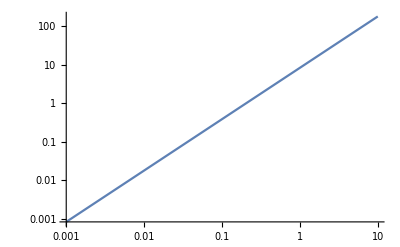

```mathematica
LogLogPlot[ff[t],{t,10^-3,10}]
```

```mathematica
RationalInterpolation
```

```mathematica
<<FunctionApproximations`
```